```mathematica
Lecture 8: Linear Algebra
```

Key linear algebra functions include:

```mathematica
{Table,MatrixForm,MatrixPlot,Dot,MatrixPower,N,Chop,Inverse,IdentityMatrix,Transpose,Det,Eigenvalues,Eigenvectors,Eigensystem,Norm,Normalize,LinearSolve,Solve,RowReduce,NullSpace,Dimensions,Orthogonalize}
```

### Exercise Subsection

a. Define BinomialMatrix[n_] be the (n+1)x(n+1) matrix with i,j entry equal to Binomial[i+j,i] where both i and j range from 0 to n.

b. Use Det to determine that this matrix has an inverse for values of n between 0 and 100 and then create an animation of MatrixPlot for the Inverse of this matrix as n ranges from 0 to 100. 

c. Let b be the vector in R^(11) with nth coordinate equal Sin[Pi n/2] for 0 <= n <= 10.  Solve the linear system BinomialMatrix[10].x = b for the vector x four different ways, once using LinearSolve, once using Inverse,  once using Solve, and once using RowReduce.

### Exercise Subsection

a. The next cell defines a function MatrixPolynomial[poly_,x_,matrix_] with input a polynomial poly in the variable x, such as x^3-x^2+4x+5, and a square matrix matrix.  What is the output?

```mathematica
MatrixPolynomial[poly_,x_,matrix_]:=Sum[Coefficient[poly,x,i] MatrixPower[matrix,i],{i,0,Exponent[poly,x]}]
```

b. Let mat be 10x10 matrix with random integer entries in between -10 and 10.  What is the result when evaluating MatrixPolynomial when taking the poly to be the CharacteristicPolynomial[mat,x] and taking matrix to be mat?

### Exercise Subsection

a. Define a function ProjectionMatrix[v__]  that has input any number of vectors of the same dimension (the double blank input v__ allows one or more vectors as input to the function because the double blank pattern matches one or more expressions) and outputs the projection matrix onto the span of the vectors in v.  

This projection matrix can be found with these steps: 
1. Use Orthogonalize to find an orthonormal basis for the span of the vectors in v (this implements the Gram-Schmidt procedure).
2. If the nonzero vectors in in the orthonormal basis are u_1,u_2,...,u_k then the desired projection matrix is Partition[u_1,1].{u_1}/(u_1.u_1)+...+Partition[u_k,1].{u_k}/(u_k.u_k)

b. Let P be the ProjectionMatrix found by selecting 5 vectors in R^10 at with random integer entries between -100 and 100 and then applying ProjectionMatrix to these 5 vectors.  Verify that the following properties hold:
1. The determinant of P is 0.
2. P^2 = P.
3. P is a symmetric matrix, meaning that P is equal to its transpose.
4. The inverse to I + P/2 is I - P/3.

### Exercise Subsection

a. Write a function RandomSymmetric[n_] which generates an n x n symmetric matrix with entries that are random real numbers between 0 and 1.

b. Define a function called TestValue[A_] that uses a Module to define a local variable x such that x is a randomly selected unit vector the correct dimension to evaluate the matrix multiplication x.A.x (see Dimensions and Normalize).  The output of TestValue is the quantity x.A.x (this quantity is the matrix multiplication x^T A x, Mathematica automatically interprets the matrix multiplication correctly without the transpose on the first vector x).

c. Let A be a fixed symmetric 5x5 matrix, generated with RandomSymmetric[5].  Estimate the maximum value of the quantity x.A.x by running TestValue[A] many times and selecting the largest output.  Compare this with the largest Eigenvalue of A.

### Exercise Subsection

Write a function RealEigenvectors with input a square matrix and output a list of linearly independent nonzero real eigenvectors of the matrix (removing any zero vectors or complex valued eigenvalues from Eigenvectors).  Additionally, any output vectors should be scaled to have length 1 (see Normalize).

```mathematica
RealEigenvectors[matrix_/;SquareMatrixQ@matrix]:=Normalize/@Cases[Eigenvectors@matrix,x_/;Element[x,Reals]&&Norm@x!=0]
```

### Exercise Subsection

Define a function PlotMatrixEffect[matrix_] where the input matrix is a 2x2 matrix.  The output should be a graphic that illustrates the effect of matrix multiplication by matrix on the unit circle and the vectors {1,0} and {0,1} in R^2.

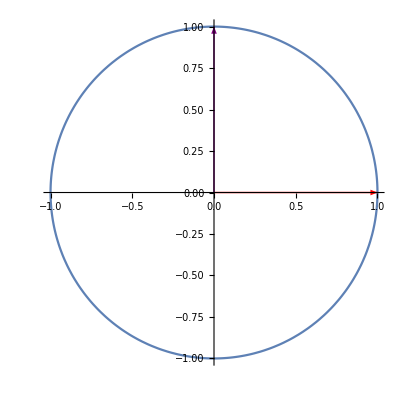
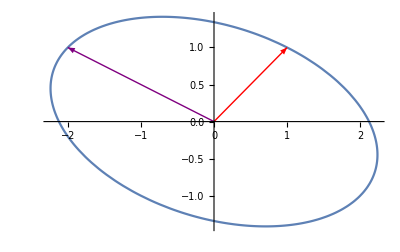

```mathematica
PlotMatrixEffect[matrix_]:=Module[{G1,G2},
G1=ParametricPlot[matrix.{Cos[t],Sin[t]},{t,0,2Pi}];
G2=Graphics@{Red,Arrow@{{0,0},matrix.{1,0}},Purple,Arrow@{{0,0},matrix.{0,1}}};
Show[G1,G2]]

{PlotMatrixEffect@IdentityMatrix@2,PlotMatrixEffect[{{1,-2},{1,1}}]}
```